# Hamasaiid model derivations

## Surface profile asperity peak height Distributions, Real(blue), Orange(Hamasaiid)

```mathematica
Quit[]
```

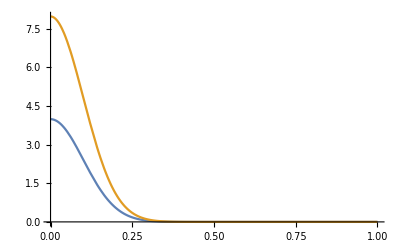

```mathematica
Show[ Plot[{(ⅇ^(-(y)^2/(2(σ)^2)))/(√(2 π) σ)/.σ-> 0.1,2(ⅇ^(-(y)^2/(2 σ^2)))/(√(2 π) σ)/.σ-> 0.1},{y,0,1},PlotRange->All]]
```

# Real distribution

```mathematica
Quit[]
```

## Height distribution ϕ_0(y)

```mathematica
Subscript[ϕ, 0]=(ⅇ^(-(y)^2/(2(Subscript[σ, 0])^2)))/(√(2 π) Subscript[σ, 0])
```

(ⅇ^(-y^2/(2 σ_0^2)))/(√(2 π) σ_0)

## Arithmetic average of absolute height deviation, R_0

```mathematica
Subscript[R, 0]=Simplify[Integrate[Subscript[ϕ, 0]*Abs[y],{y,-Infinity,Infinity}],{Subscript[σ, 0]>0,Subscript[σ, 0]∈Reals}]
```

√(2/π) σ_0

## Mean μ_0

```mathematica
Subscript[μ, 0]=0
```

0

## Standard deviation σ_0

```mathematica
Subscript[σ, 0]=Simplify[Sqrt[Integrate[Subscript[ϕ, 0]*(y-Subscript[μ, 0])^2,{y,-Infinity,Infinity}]],{Subscript[σ, 0]>0,Subscript[σ, 0]∈Reals}]
```

σ_0

## Surface area of bases of valleys/peaks + gaps, A_0, given by number of valleys/peaks, N_0, height distribution ϕ_0, and valley/peak slope m_0

```mathematica
Subscript[A, 0]=Simplify[ϵ*Subscript[N, 0]*2*(Integrate[Subscript[ϕ, 0]*Pi*(y/Subscript[m, 0])^2,{y,0,Infinity}]),{Subscript[σ, 0]>0,Subscript[σ, 0]∈Reals}]
```

(π ϵ N_0 σ_0^2)/m_0^2

## Density of peaks/valleys over surface area, n_0

```mathematica
Subscript[n, 0]=Subscript[N, 0]/Subscript[A, 0]
```

m_0^2/(π ϵ σ_0^2)

## Average diameter of circular base, B_0

```mathematica
Subscript[B, 0]=2/Subscript[m, 0]*Simplify[Integrate[Subscript[ϕ, 0]*Abs[y],{y,-Infinity,Infinity}],{Subscript[σ, 0]>0,Subscript[σ, 0]∈Reals}]
```

(2 √(2/π) σ_0)/m_0

## Slope, m_0, given by mean peak spacing L_0 = B_0

```mathematica
Solve[Subscript[L, 0]==(2 √(2/π) Subscript[σ, 0])/Subscript[m, 0],Subscript[m, 0]]
```

{{m_0→(2 √(2/π) σ_0)/L_0}}

# Hamasaiid distribution

```mathematica
Quit[]
```

## Height distribution ϕ_1(y)

```mathematica
Subscript[ϕ, 1]=2(ⅇ^(-(y)^2/(2(Subscript[σ, 0])^2)))/(√(2 π) Subscript[σ, 0])
```

(ⅇ^(-y^2/(2 σ_0^2)) √(2/π))/σ_0

## Arithmetic average of absolute height deviation, R_1

```mathematica
Subscript[R, 1]=Simplify[Integrate[Subscript[ϕ, 1]*y,{y,0,Infinity}],{Subscript[σ, 0]>0,Subscript[σ, 0]∈Reals}]
```

√(2/π) σ_0

## Mean, μ_1

```mathematica
Subscript[μ, 1]=Subscript[R, 1]
```

√(2/π) σ_0

## Standard deviation from mean μ_1, σ_1

```mathematica
Subscript[σ, 1]=Simplify[Sqrt[Integrate[Subscript[ϕ, 1]*(y-Subscript[μ, 1])^2,{y,0,Infinity}]],{Subscript[σ, 0]>0,Subscript[σ, 0]∈Reals}]
```

√((-2+π)/π) σ_0

## Surface area of bases of peaks + gaps, A_1, given by number of valleys and peaks, N_1, height distribution ϕ_1, and peak slope m_1

```mathematica
Subscript[A, 1]=Simplify[ϵ*Subscript[N, 1]*(Integrate[Subscript[ϕ, 1]*Pi*(y/Subscript[m, 1])^2,{y,0,Infinity}]),{Subscript[σ, 0]>0,Subscript[σ, 0]∈Reals}]
```

(π ϵ N_1 σ_0^2)/m_1^2

## Density of peaks over surface area, n_1

```mathematica
Subscript[n, 1]=Subscript[N, 1]/Subscript[A, 1]
```

m_1^2/(π ϵ σ_0^2)

## Average diameter of circular base, B_1

```mathematica
Subscript[B, 1]=2/Subscript[m, 1]*Simplify[Integrate[Subscript[ϕ, 1]*y,{y,0,Infinity}],{Subscript[σ, 0]>0,Subscript[σ, 0]∈Reals}]
```

(2 √(2/π) σ_0)/m_1

## Slope, m_1, given by mean peak spacing, L_0

```mathematica
Solve[Subscript[L, 0]==(2 √(2/π) Subscript[σ, 0])/Subscript[m, 1],{Subscript[m, 1]}]
```

{{m_1→(2 √(2/π) σ_0)/L_0}}

```mathematica
Subscript[m, 1]=(2 √(2/π) Subscript[σ, 0])/Subscript[L, 0]
```

(2 √(2/π) σ_0)/L_0

## Updated n_1

```mathematica
Subscript[n, 1]
```

8/(π^2 ϵ L_0^2)

## Density of microcontact spots, n_(s,1)

```mathematica
Subscript[n, s,1]=Subscript[n, 1]*Simplify[Integrate[Subscript[ϕ, 1],{y,Y,Infinity}],{Subscript[σ, 0]>0,Subscript[σ, 0]∈Reals}]
```

(8 Erfc[Y/(√2 σ_0)])/(π^2 ϵ L_0^2)

## Average projected radius of contact area, a_(s,1), which exceeds entrapped air thickness, Y

```mathematica
Subscript[a, s,1]=Simplify[Integrate[(y-Y)/Subscript[m, 1]*Subscript[ϕ, 1],{y,Y,Infinity}],{Subscript[σ, 0]>0,Subscript[σ, 0]∈Reals}]
```

1/4 L_0 (2 ⅇ^(-Y^2/(2 σ_0^2))+(√(2 π) Y (-1+Erf[Y/(√2 σ_0)]))/σ_0)

## Average radius of circular base, b_s

```mathematica
Subscript[b, s]=Subscript[L, 0]/2
```

L_0/2

# Plot Abbott-Firestone curve, L_0=128e-6, σ_0=0.58e-6,ϵ=1.5

```mathematica
Quit[]
```

## Measured Abott-firestone by Hamasaiid et al.

```mathematica
data = {{0,1.8463428571428571*^-6},{0.01109350237717907,1.6251428571428572*^-6},{0.026941362916006323,1.471657142857143*^-6},{0.053882725832012646,1.309142857142857*^-6},{0.08716323296354991,1.182742857142857*^-6},{0.12678288431061804,1.0608571428571428*^-6},{0.16640253565768623,9.660571428571426*^-7},{0.20919175911251978,8.848*^-7},{0.2488114104595879,8.215999999999999*^-7},{0.3090332805071315,7.403428571428573*^-7},{0.38193343898573695,6.500571428571428*^-7},{0.4548335974643424,5.507428571428572*^-7},{0.5309033280507132,4.6045714285714254*^-7},{0.6307448494453249,3.2954285714285667*^-7},{0.7036450079239303,2.3925714285714286*^-7},{0.7876386687797148,1.3994285714285725*^-7},{0.8478605388272582,6.320000000000009*^-8},{0.9033280507131537,1.8057142857142762*^-8},{0.96513470681458,0}};
```

## Helper function to transpose x and y axi

```mathematica
axisFlip=#/.{x_Line|x_GraphicsComplex:>MapAt[#~Reverse~2&,x,1],x:(PlotRange->_):>x~Reverse~2}&;
```

## Modeled a_s/b_s

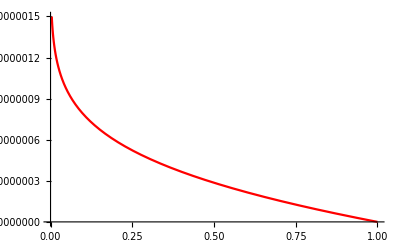

```mathematica
abfs=Plot[1/2 (2 ⅇ^(-Y^2/(2 Subscript[σ, 0]^2))+(√(2 π) Y (-1+Erf[Y/(√2 Subscript[σ, 0])]))/Subscript[σ, 0])/.{Subscript[σ, 0]->0.578*^-6, Subscript[L, 0]-> 128.5*^-6},{Y,0,1.5*^-6}, PlotStyle-> Red] // axisFlip
```

## Measured Abbott firestone(Red) vs model (Blue)

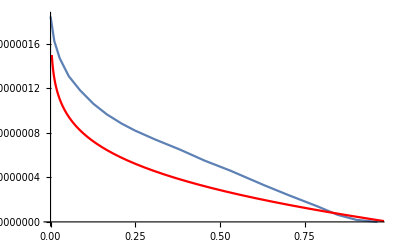

```mathematica
Show[ListLinePlot[data],abfs]
```

# Plot HTC(y)

```mathematica
Quit[]
```

## Initialize values for a_(s,2) , n_(s,2) , a_(s,1) , n_(s,1)

```mathematica
Subscript[a, s,1]=1/4 Subscript[L, 0] (2 ⅇ^(-Y^2/(2 Subscript[σ, 0]^2))+(√(2 π) Y (-1+Erf[Y/(√2 Subscript[σ, 0])]))/Subscript[σ, 0]);
Subscript[n, s,1]=(8 Erfc[Y/(√2 Subscript[σ, 0])])/(π^2 ϵ Subscript[L, 0]^2);
```

```mathematica
Subscript[b, s]=Subscript[L, 0]/2;
```

## Effective heat transfer coefficient λ_s

```mathematica
Subscript[λ, s]=2*Subscript[λ, 1]*Subscript[λ, 2]/(Subscript[λ, 1]+Subscript[λ, 2])
```

(2 λ_1 λ_2)/(λ_1+λ_2)

## Peak heat transfer coefficient, h

```mathematica
TraditionalForm[Subscript[h, 1]=(2 Subscript[λ, s] Subscript[n, s,1] Subscript[a, s,1])/(1-Subscript[a, s,1]/Subscript[b, s])^1.5];
```

```mathematica
h(Y)=(8 Subscript[λ, 1] Subscript[λ, 2] ((√(2 π) Y (erf(Y/(√2 Subscript[σ, 0]))-1))/Subscript[σ, 0]+2 ⅇ^(-Y^2/(2 Subscript[σ, 0]^2))) erfc(Y/(√2 Subscript[σ, 0])))/(π^2 (Subscript[λ, 1]+Subscript[λ, 2]) Subscript[L, 0] ϵ (1/2 (-(√(2 π) Y (erf(Y/(√2 Subscript[σ, 0]))-1))/Subscript[σ, 0]-2 ⅇ^(-Y^2/(2 Subscript[σ, 0]^2)))+1)^1.5);
```

## Plot peak heat transfer coefficient, h as a function of air gap width Y

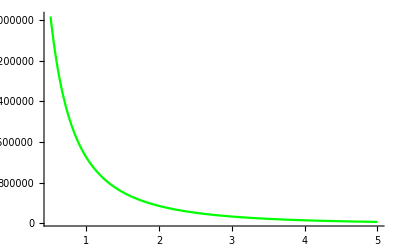

```mathematica
hplot1=Plot[(8 Subscript[λ, 1] Subscript[λ, 2] ((√(2 π) Y (erf(Y/(√2 Subscript[σ, 0]))-1))/Subscript[σ, 0]+2 ⅇ^(-Y^2/(2 Subscript[σ, 0]^2))) erfc(Y/(√2 Subscript[σ, 0])))/(π^2 (Subscript[λ, 1]+Subscript[λ, 2]) Subscript[L, 0] ϵ (1/2 (-(√(2 π) Y (erf(Y/(√2 Subscript[σ, 0]))-1))/Subscript[σ, 0]-2 ⅇ^(-Y^2/(2 Subscript[σ, 0]^2)))+1)^1.5)/.{Subscript[λ, 1]-> 29, Subscript[λ, 2]->70, Subscript[σ, 0]->0.578*^-6, ϵ-> 1.5, Subscript[L, 0]-> 128.5*^-6},{Y,0,0.5*^-6},PlotStyle->Green];

Show[hplot1 ,PlotRange-> Automatic]
```

## Peak heat transfer coefficient h using values by Hamasaiid (without capillary pressure)

```mathematica
Subscript[h, 1]=(2 Subscript[λ, s] Subscript[n, s,1] Subscript[a, s,1])/(1-Subscript[a, s,1]/Subscript[b, s])^1.5/.{Subscript[λ, 1]-> 29, Subscript[λ, 2]->70, Subscript[σ, 0]->0.578*^-6, ϵ-> 1.5, Subscript[L, 0]-> 128.5*^-6, Y-> 0.164*^-6}
```

516922.

# Calculate initial air gap thickness Y_0

```mathematica
Quit[]
```

## Ideal gas law for air thickness

```mathematica
(Subscript[P, 1]-Subscript[P, γ])Subscript[V, 1]/Subscript[T, 1]==Subscript[P, 0] Subscript[V, 0]/Subscript[T, 0]
```

((P_1-P_γ) V_1)/T_1==(P_0 V_0)/T_0

## Re-initialize slopes

```mathematica
Subscript[m, 1]=(2 √(2/π) Subscript[σ, 0])/Subscript[L, 0];
```

## Re-initialize distribution functions

```mathematica
Subscript[ϕ, 1]=2(ⅇ^(-(y)^2/(2(Subscript[σ, 0])^2)))/(√(2 π) Subscript[σ, 0]);
```

## Initial volume for cone-shaped air pocket, V_0

```mathematica
Subscript[V, 0,1]=Simplify[Integrate[{1/3*Pi/Subscript[m, 1]^2 *Subscript[ϕ, 1]*y^3},{y,0,Infinity}],{Subscript[σ, 0]>0,Subscript[σ, 0]∈Reals}]
```

{(π^(3/2) L_0^2 σ_0)/(6 √2)}

## Final volume for cone-shaped air pocket, V_1

```mathematica
Subscript[V, 1,1]=1/3*Pi*Subscript[Y, 0,1]^3/Subscript[m, 1]^2
```

(π^2 L_0^2 Y_(0,1)^3)/(24 σ_0^2)

## Solve initial air layer thickness, Y_0

```mathematica
Simplify[Solve[(Subscript[P, 1]-Subscript[P, γ])/Subscript[T, 1]* (π^2 Subscript[L, 0]^2 Subscript[Y, 0,1]^3)/(24 Subscript[σ, 0]^2)==(Subscript[P, 0] Subscript[V, 0,1])/Subscript[T, 0],{Subscript[Y, 0,1]}]]
```

{{Y_(0,1)→(√2 P_0^(1/3) σ_0^(1/3))/(π^(1/6) (((P_1-P_γ) T_0)/(T_1 σ_0^2))^(1/3))},{Y_(0,1)→-((-1)^(1/3) √2 P_0^(1/3) σ_0^(1/3))/(π^(1/6) (((P_1-P_γ) T_0)/(T_1 σ_0^2))^(1/3))},{Y_(0,1)→((-1)^(2/3) √2 P_0^(1/3) σ_0^(1/3))/(π^(1/6) (((P_1-P_γ) T_0)/(T_1 σ_0^2))^(1/3))}}

```mathematica
Subscript[Y, 0,1]=(√2 Subscript[P, 0]^(1/3) Subscript[σ, 0]^(1/3))/(π^(1/6) (((Subscript[P, 1]-Subscript[P, γ]) Subscript[T, 0])/(Subscript[T, 1] Subscript[σ, 0]^2))^(1/3))
```

(√2 P_0^(1/3) σ_0^(1/3))/(π^(1/6) (((P_1-P_γ) T_0)/(T_1 σ_0^2))^(1/3))

# Determine Y_t, Y as a function of time

```mathematica
Quit[]
```

## Fitting coefficient, C_0

```mathematica
Subscript[C, 0,1]=Subscript[V, al,1]*Subscript[n, s,1]*1/2
```

(√2 Erfc[P_0^(1/3)/(π^(1/6) (((P_1-P_γ) T_0)/(T_1 σ_0^2))^(1/3) σ_0^(2/3))] (π^(1/3)+((-1+ⅇ^(-P_0^(2/3)/(π^(1/3) (((P_1-P_γ) T_0)/T_1)^(2/3)))) P_0^(2/3))/(((P_1-P_γ) T_0)/T_1)^(2/3)) σ_0)/(3 π^(5/6) ϵ)

## Volume of aluminum inside asperities, V_al

```mathematica
Subscript[V, al,1]=Simplify[1/3*Pi*1/(Subscript[m, 1])^2*Integrate[Subscript[ϕ, 1]*y^3,{y,0,Infinity}]-1/3*Pi*(Subscript[Y, 0,1]/Subscript[m, 1])^2*Integrate[Subscript[ϕ, 1]*y,{y,0,Subscript[Y, 0,1]}],{Subscript[σ, 0]>0,Subscript[σ, 0]∈Reals}]
```

(π^(7/6) L_0^2 (π^(1/3)+((-1+ⅇ^(-P_0^(2/3)/(π^(1/3) (((P_1-P_γ) T_0)/T_1)^(2/3)))) P_0^(2/3))/(((P_1-P_γ) T_0)/T_1)^(2/3)) σ_0)/(6 √2)

## Time dependent air gap thickness, Y_t

```mathematica
Subscript[Y, t,1]=Subscript[Y, 0,1]+2*Subscript[C, 0,1]*Subscript[h, 1]*(Subscript[T, 2]-Subscript[T, 3])/(ρ*L*S)*t
```

(√2 P_0^(1/3) σ_0^(1/3))/(π^(1/6) (((P_1-P_γ) T_0)/(T_1 σ_0^2))^(1/3))+(16 √2 t Erfc[P_0^(1/3)/(π^(1/6) (((P_1-P_γ) T_0)/(T_1 σ_0^2))^(1/3) σ_0^(2/3))]^2 (π^(1/3)+((-1+ⅇ^(-P_0^(2/3)/(π^(1/3) (((P_1-P_γ) T_0)/T_1)^(2/3)))) P_0^(2/3))/(((P_1-P_γ) T_0)/T_1)^(2/3)) (T_2-T_3) λ_1 λ_2 (2 ⅇ^(-P_0^(2/3)/(π^(1/3) (((P_1-P_γ) T_0)/(T_1 σ_0^2))^(2/3) σ_0^(4/3)))+(2 π^(1/3) (-1+Erf[P_0^(1/3)/(π^(1/6) (((P_1-P_γ) T_0)/(T_1 σ_0^2))^(1/3) σ_0^(2/3))]) P_0^(1/3))/((((P_1-P_γ) T_0)/(T_1 σ_0^2))^(1/3) σ_0^(2/3))) σ_0)/(3 L π^(17/6) S ϵ^2 ρ L_0 (λ_1+λ_2) (1+1/2 (-2 ⅇ^(-P_0^(2/3)/(π^(1/3) (((P_1-P_γ) T_0)/(T_1 σ_0^2))^(2/3) σ_0^(4/3)))-(2 π^(1/3) (-1+Erf[P_0^(1/3)/(π^(1/6) (((P_1-P_γ) T_0)/(T_1 σ_0^2))^(1/3) σ_0^(2/3))]) P_0^(1/3))/((((P_1-P_γ) T_0)/(T_1 σ_0^2))^(1/3) σ_0^(2/3))))^1.5)

# Determine h as a function of time

```mathematica
Quit[]
```

## Calculate relevant quantities

```mathematica
Subscript[ϕ, 1]=2(ⅇ^(-(y)^2/(2(Subscript[σ, 0])^2)))/(√(2 π) Subscript[σ, 0]);
Subscript[Y, 0,1]=(√2 Subscript[P, 0]^(1/3) Subscript[σ, 0]^(1/3))/(π^(1/6) (((Subscript[P, 1]-Subscript[P, γ]) Subscript[T, 0])/(Subscript[T, 1] Subscript[σ, 0]^2))^(1/3));
Subscript[C, 0,1]=Subscript[V, al,1]*Subscript[n, s,1]*1/2;
Subscript[V, al,1]=Simplify[1/3*Pi*1/(Subscript[m, 1])^2*Integrate[Subscript[ϕ, 1]*y^3,{y,0,Infinity}]-1/3*Pi*(Subscript[Y, 0,1]/Subscript[m, 1])^2*Integrate[Subscript[ϕ, 1]*y,{y,0,Subscript[Y, 0,1]}],{Subscript[σ, 0]>0,Subscript[σ, 0]∈Reals}];
Subscript[Y, t,1]=Subscript[Y, 0,1]+2*Subscript[C, 0,1]*Subscript[h, 1]*(Subscript[T, 2]-Subscript[T, 3])/(ρ*L*S)*t;
Subscript[a, t,1]=1/4 Subscript[L, 0] (2 ⅇ^(-Subscript[Y, t,1]^2/(2 Subscript[σ, 0]^2))+(√(2 π) Subscript[Y, t,1](-1+Erf[Subscript[Y, t,1]/(√2 Subscript[σ, 0])]))/Subscript[σ, 0]);
Subscript[n, t,1]=(8 Erfc[Subscript[Y, t,1]/(√2 Subscript[σ, 0])])/(π^2 ϵ Subscript[L, 0]^2);
Subscript[h, t,1]=(2 Subscript[λ, s] Subscript[n, t,1] Subscript[a, t,1])/(1-Subscript[a, t,1]/Subscript[b, s])^1.5;
Subscript[a, s,1]=1/4 Subscript[L, 0] (2 ⅇ^(-Subscript[Y, 0,1]^2/(2 Subscript[σ, 0]^2))+(√(2 π) Subscript[Y, 0,1] (-1+Erf[Subscript[Y, 0,1]/(√2 Subscript[σ, 0])]))/Subscript[σ, 0]);
Subscript[n, s,1]=(8 Erfc[Subscript[Y, 0,1]/(√2 Subscript[σ, 0])])/(π^2 ϵ Subscript[L, 0]^2);
Subscript[h, 1]=(2 Subscript[λ, s] Subscript[n, s,1] Subscript[a, s,1])/(1-Subscript[a, s,1]/Subscript[b, s])^1.5;
Subscript[λ, s]=2*Subscript[λ, 1]*Subscript[λ, 2]/(Subscript[λ, 1]+Subscript[λ, 2]);
Subscript[b, s]=Subscript[L, 0]/2;
Subscript[m, 1]=(2 √(2/π) Subscript[σ, 0])/Subscript[L, 0];
```

## Hamasaiid model for time-evolution of Al-alloy IHTC

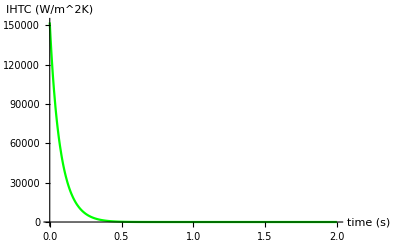

```mathematica
Plot[(2 Subscript[λ, s] Subscript[n, t,1] Subscript[a, t,1])/(1-Subscript[a, t,1]/Subscript[b, s])^1.5/.{ Subscript[σ, 0]->0.578*^-6, Subscript[L, 0]-> 128.7*^-6,  Subscript[λ, 1]-> 29, Subscript[λ, 2]->109, ϵ-> 1.5, Subscript[P, γ]-> 0.87*26*^6,  Subscript[P, 1]->26*^6, Subscript[P, 0]->1.013*^5,  Subscript[T, 0]->300, Subscript[T, 1] -> 860, Subscript[T, 2]->853, Subscript[T, 3]->453,ρ->2810,  S->4*^-3, L-> 389*^3},{t,0,2},PlotStyle->Green, PlotRange -> Full, AxesLabel->{"time (s)","IHTC (W/m^2K)"}]
```

## Hamasaiid model for time evolution of Mg-alloy IHTC

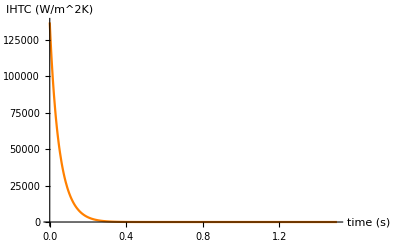

```mathematica
Plot[Evaluate[(2 Subscript[λ, s] Subscript[n, t,1] Subscript[a, t,1])/(1-Subscript[a, t,1]/Subscript[b, s])^1.5/.{ Subscript[σ, 0]->0.578*^-6, Subscript[L, 0]-> 128*^-6,  Subscript[λ, 1]-> 29, Subscript[λ, 2]->70, ϵ-> 1.5, Subscript[P, γ]-> 0.87*26*^6,  Subscript[P, 1]->26*^6, Subscript[P, 0]->1.013*^5,  Subscript[T, 0]->300, Subscript[T, 1] -> 860, Subscript[T, 2]->853, Subscript[T, 3]->453,ρ->1810,  S->4*^-3, L-> 370*^3}],{t,0,1.5},PlotStyle->Orange,  PlotRange -> Full,AxesLabel->{"time (s)","IHTC (W/m^2K)"}]
```

## Estimate peak IHTC for Al

```mathematica
Subscript[h, t,1]/.{ Subscript[σ, 0]->0.578*^-6, Subscript[L, 0]-> 128.7*^-6,  Subscript[λ, 1]-> 29, Subscript[λ, 2]->109, ϵ-> 1.5, Subscript[P, γ]-> 0.87*26*^6,  Subscript[P, 1]->26*^6, Subscript[P, 0]->1.013*^5,  Subscript[T, 0]->300, Subscript[T, 1] -> 860, Subscript[T, 2]->853, Subscript[T, 3]->453,ρ->2810,  S->4*^-3, L-> 389*^3, t-> 0}
```

152095.

## Estimate peak IHTC for Mg

```mathematica
Subscript[h, t,1]/.{ Subscript[σ, 0]->0.578*^-6, Subscript[L, 0]-> 128.5*^-6,  Subscript[λ, 1]-> 29, Subscript[λ, 2]->70, ϵ-> 1.5, Subscript[P, γ]-> 0.87*26*^6,  Subscript[P, 1]->26*^6, Subscript[P, 0]->1.013*^5,  Subscript[T, 0]->300, Subscript[T, 1] -> 860, Subscript[T, 2]->853, Subscript[T, 3]->453,ρ->1810,  S->4*^-3, L-> 370*^3, t-> 0}
```

136366.

# Surface energy

```mathematica
Quit[]
```

## Young’s Equation

```mathematica
Subscript[γ, 1]*Cos[θ] = Subscript[γ, 1]-Subscript[γ, 12]
```

## Capillary Force in notch (good wetting)

```mathematica
Subscript[F, c]=2*Subscript[γ, 1]*Sin[θ+ϕ]/(Subscript[r, 0]-x*Cot[ϕ])
```

(2 Sin[θ+ϕ] γ_1)/(-x Cot[ϕ]+r_0)

## Absolute values of capillary pressure model by Chao Yuan et al.

```mathematica
Subscript[P, γ]=2*γ*Sin[θ+ϕ]/(Y*Cot[ϕ])/.{γ-> 0.9,ϕ-> ArcTan[(2 √(2/π) 0.578*^-6)/(128.7*^-6)], Y-> 3.5*^-7,Subscript[σ, 0]->0.578*^-6, Subscript[L, 0]-> 128.7*^-6,θ-> Pi/6}
```

18656.9

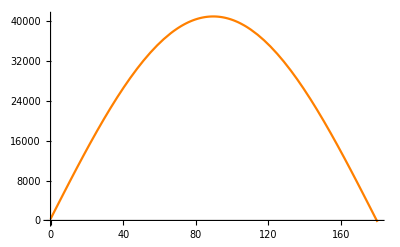

```mathematica
Plot[2*γ*Sin[θ Degree+ϕ]/(Y*Cot[ϕ])/.{γ-> 1,ϕ-> ArcTan[(2 √(2/π) 0.578*^-6)/(128.7*^-6)], Y-> 3.5*^-7,Subscript[σ, 0]->0.578*^-6, Subscript[L, 0]-> 128.7*^-6},{θ,0,180},PlotStyle->Orange, PlotRange -> Automatic]
```

# Water hammer pressure

## Aluminum gate

```mathematica
P=ρ*c*V*Sin[x]/.{ρ-> 2810, c-> 3840, V-> 1.931, x-> 3.5°};
N[P]
```

1.27202×10^6

## Mercury gate

```mathematica
P=ρ*c*V*Sin[x]/.{ρ-> 1810, c-> 3357.19, V-> 2.867, x-> 3.5°}
```

1.06355×10^6

## Wave velocity aluminum

```mathematica
c=Evaluate[(E/ρ)^(1/2)/.{ρ-> 2800, E-> 41.3*^9}]//N
```

3840.57

## Wave velocity magnesium

```mathematica
c=Evaluate[(E/ρ)^(1/2)/.{ρ-> 1810, E-> 20.4*^9}]//N
```

3357.19

# Stagnation pressure

```mathematica
P=1/2*ρ*V^2/.{ρ-> 2570, V-> 4}
```

20560